Last modified on: Tuesday, July 10, 2018 at 22:52

Author Info

Yash Akhauri

Sebastian Bodenstein

BITS Pilani

Poster Session Content

Introducing Hadamard Binary Neural Networks

1) Develop high performance kernels for HBNN operations.
2) Implement HBNN MLP in Wolfram Language, and inspect its performance on the MNIST dataset.
3) Study the high dimensional geometry of HBNNs.
4) Solve the scalability deadlock of InnerProduct.

Add the most representative image of your project here. (We recommend just 1 image, if you add more, we will make a collage of the images.)

-Graphics-

1) Faster convergence with respect to vanilla binarization techniques.
2) Consistently 10 times faster than CMMA algorithm. 
3) At par with MKL GEMM with minimal optimization.
4) Angle of randomly initialized vectors preserved in high dimensional spaces. (Approximately 37 degrees as vector length approach infinity.)
5) Histogram has greater granularity than Binary Neural Networks.

1) Conduct a study of the communication costs associated with this architecture.
2) Implement im2col convolution methods with low memory overhead.
3) Test accuracy on deep convolutional and language models.
4) Develop a distributed framework optimized for AI training.

Note: Everything above this bar is your poster.Make sure it fits on a single page. "Preview Poster"

End of School Presentation Content

In addition to the poster content, include other content to present at the 2 minute presentation for end of school. Use the buttons below to add more sections."Add Header""Add Text""Add Code or Image"

An analysis of Hadamard Binary Neural Networks

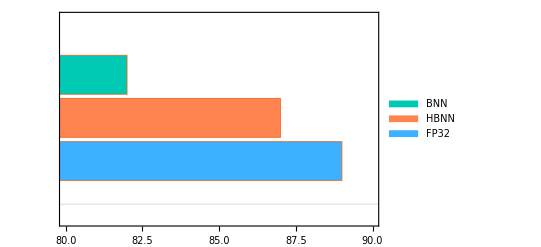
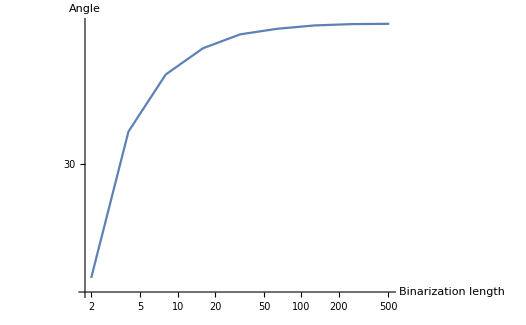
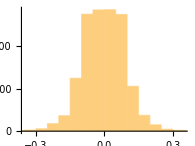
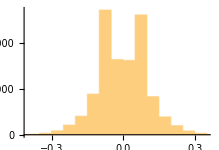
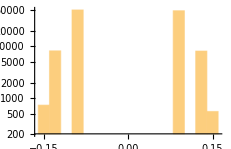
-Graphics-
Accuracy on MNIST
 -Graphics-
Performance analysis 
-Graphics--Graphics-
Angle Preservation property
-Graphics-
Weight histogram analysis
	      Full Precision	       Hadamard BNN	      	   	      	         BNN
-Graphics--Graphics--Graphics-

Note: Everything above this bar is in your 2 minute presentation. Make sure it fits on 2 slides. "Preview Presentation"

Detailed Project Notes

#### Main Results in Detail

Deep neural networks are an important tool in modern applications. It has become a major challenge to accelerate their training. As the complexity of our training tasks increase, the computation does too. For sustainable machine learning at scale, we need distributed systems that can leverage the available hardware effectively. This research hopes to exceed the current state of the art performance of neural networks by introducing a new architecture optimized for distributability. The scope of this work is not just limited to optimizing neural network training for large servers, but also to bring training to heterogeneous environments; paving way for a distributed peer to peer mesh computing platform that can harness the wasted resources of idle computers in a workplace for AI.
  
  Advantages of Hadamard Binarization
1. Faster convergence with respect to vanilla binarization techniques.
  2. Consistently about 10 times faster than CMMA algorithm.
  3. Angle of randomly initialized vectors preserved in high dimensional spaces. (Approximately 37 degrees as vector length approach infinity.)
4. Reduced communication times for distributed deep learning.
  5. Optimization of im2col algorithm for faster inference.
  6. Reduction of model sizes.
  
  The HBNN model gives 87 % accuracy, whereas the BNN model (Binary Neural Networks) give only 82 %. These networks have only been trained for 5 epochs.
  Hadamard BNN preserves the distribution of the weights much better.
  Binarization approximately preserves the direction of high dimensional vectors. The figure above demonstrates that the angle between a random vector (from a standard normal distribution) and its binarized version converges to ~ 37 degrees as the dimension of the vector goes to infinity. This angle is exceedingly small in high dimensions.

#### Code

GitHub links:

https://github.com/akhauriyash/Summer2018Starter

https://github.com/akhauriyash/Hadamard-Nets

## Building the net

#### MNIST Data fetch

```mathematica
prepareData[]:= Module[{tx, tt, ty,txT, ttT, tyT, i, training, testing}, 
training = RandomSample[ExampleData[{"MachineLearning","MNIST"},"TrainingData"]];
testing = RandomSample[ExampleData[{"MachineLearning", "MNIST"}, "TestData"]];
txT = ArrayReshape[Map[ImageData, testing[[;;, 1]]], {10000, 784}];
ttT = testing[[;;, 2]];
tyT = ConstantArray[0, {10000, 10}];
For[i = 1, i≤10000, i++, tyT[[i, 1+ttT[[i]]]] = 1;];
tx = ArrayReshape[Map[ImageData, training[[;;, 1]]], {60000, 784}];
tt  = training[[;;, 2]];
ty = ConstantArray[0, {60000, 10}];
For[i = 1, i≤60000, i++, ty[[i, 1+tt[[i]]]] = 1;]; Return[{tx, ty, txT, tyT}];];
{input, target, testinp, testtar} = prepareData[];
```

#### Xavier Initialization of network

```mathematica
initializeWeights[hiddennodes1_, hiddennodes2_, outputnodes_] := Module[{mininet, netinit, w0, w1, w2},
mininet = NetChain[{LinearLayer[hiddennodes1], Ramp,LinearLayer[hiddennodes2], Ramp, LinearLayer[outputnodes], LogisticSigmoid}, "Input"->784];
netinit = NetInitialize[mininet, Method ->{"Xavier"}];
w0 = Transpose@NetExtract[netinit, {All, "Weights"}][[1]];
w1 = Transpose@NetExtract[netinit, {All, "Weights"}][[3]];
w2 = Transpose@NetExtract[netinit, {All, "Weights"}][[5]];
Return[{w0, w1, w2}];];
```

#### Define Network Variables

```mathematica
learningrate = 0.00003;
binAggression = 4;
hiddennodes1 = 128;
hiddennodes2 = 128;
outputnodes = 10;
batchsize = 8;
iterations = Floor[60000/batchsize];
epochs = 5;
b1 = 0.9;
b2 = 0.999;
epsilon = 0.00000001;
inputdim  = 784;
```

#### Hadamard Binarization functions

```mathematica
hbGradForward[x_, hBL_] :=Module[{row, col,tempMat, matCreate, joinerMat, x2}, 
x2 = x;
For[col = 1, col ≤ Dimensions[x2][[2]], col++,matCreate = Abs[ArrayReshape[x2[[;;, col]], {Ceiling[Dimensions[x2][[1]]/hBL],hBL}, 0]];
tempMat = Map[Max, matCreate[[;;-2, ;;]], {1}];
If[Mod[Dimensions[x2][[1]], hBL]≠ 0,
AppendTo[tempMat, Max[matCreate[[-1, ;;]]]],
AppendTo[tempMat, Max[matCreate[[-1, ;;]]]]];
For[row = 1, row ≤ Dimensions[x2][[1]], row++,
x2[[row, col]] = Sign[x2[[row, col]]]*tempMat[[Ceiling[row/hBL]]];
];
];
Return[x2]];
hbBackward[x_] := Return[Clip[x, {-1, 1}, {0, 0}]];
hbWForward[x_, hBL_] :=Module[{row, col,tempMat, matCreate, joinerMat, x2}, 
x2 = x;
For[col = 1, col ≤ Dimensions[x2][[2]], col++,matCreate = Abs[ArrayReshape[x2[[;;, col]], {Ceiling[Dimensions[x2][[1]]/hBL],hBL}, 0]];
tempMat = Map[Mean, matCreate[[;;-2, ;;]], {1}];
If[Mod[Dimensions[x2][[1]], hBL]≠ 0,
AppendTo[tempMat, Total[matCreate[[-1, ;;]]]/Mod[Dimensions[x2][[1]], hBL]],
AppendTo[tempMat, Mean[matCreate[[-1, ;;]]]]];
For[row = 1, row ≤ Dimensions[x2][[1]], row++,
x2[[row, col]] = Sign[x2[[row, col]]]*tempMat[[Ceiling[row/hBL]]];
];
];
Return[x2]];
hbActForward[x_, hBL_] :=Module[{row, col,tempMat, matCreate, joinerMat, x2}, 
x2 = Transpose[x];
For[col = 1, col ≤ Dimensions[x2][[2]], col++,matCreate = Abs[ArrayReshape[x2[[;;, col]], {Ceiling[Dimensions[x2][[1]]/hBL],hBL}, 0]];
tempMat = Map[Mean, matCreate[[;;-2, ;;]], {1}];
If[Mod[Dimensions[x2][[1]], hBL]≠ 0,
AppendTo[tempMat, Total[matCreate[[-1, ;;]]]/Mod[Dimensions[x2][[1]], hBL]],
AppendTo[tempMat, Mean[matCreate[[-1, ;;]]]]];
For[row = 1, row ≤ Dimensions[x2][[1]], row++,
x2[[row, col]] = Sign[x2[[row, col]]]*tempMat[[Ceiling[row/hBL]]];
];
];
Return[Transpose[x2]]];
```

#### Derivative Functions

```mathematica
sigmDeriv[x_] := Return[x*(1-x)];
rampDeriv[x_] := Return[UnitStep[x]];
```

#### Layer Evaluator Function

```mathematica
layerEval[x_, layer_Association]:=layerEval[x, Lookup[layer, "LayerType"], Lookup[layer,"Parameters"]];
layerEval[x_, "Sigmoid", param_]:= 1/(1+Exp[-x]);
layerEval[x_, "Ramp", param_] := Abs[x]*UnitStep[x];
layerEval[ x_, "LinearLayer", param_]:= Dot[x, param["Weights"]];
layerEval[ x_, "BinLayer", param_]:= Dot[hbActForward[x, binAggression], hbWForward[param["Weights"], binAggression]];
layerEval[x_, "BinarizeLayer", param_]:= hbActForward[x, binAggression];
netEvaluate[net_, x_, "Training"] := FoldList[layerEval, x, net];
netEvaluate[net_, x_, "Test"] := Fold[layerEval, x, net];
```

#### Back Propogation Algorithm

```mathematica
backProp[fullnet_, w0_, w1_, w2_, input_, target_, l3M_, l3V_,  l2M_, l1M_, l2V_, l1V_ , iteration_, lr_]:=Module[{l3Error, l3Delta, l2Error, l2Delta, l1Error, l1Delta, g2, g1, g0, l0, l1, l2, l3, l1MC, l1VC, l2MC, l2VC, l3MC, l3VC, l3MT, l2MT, l1MT, l3VT, l2VT, l1VT, w2T, w1T, w0T, w2UDT,  w1UDT, w0UDT},

l3MT = l3M; l3VT = l3V; 
l2MT = l2M; l2VT = l2V;
l1MT = l1M; l1VT = l1V;
w2T = w2; w1T = w1; w0T = w0;

l3Error = fullnet[[-1]] - target;
l3Delta = l3Error*sigmDeriv[fullnet[[-1]]];  (*Works*)
l2Error = hbBackward[Dot[hbActForward[l3Delta], Transpose@hbWForward[w2, binAggression]]];          (*Works*)
l2Delta = l2Error*rampDeriv[fullnet[[6]]];  (*Works*)
l1Error = hbBackward[Dot[hbActForward[l2Delta], Transpose@hbWForward[w1, binAggression]]];  (*Works*)
l1Delta = l1Error*rampDeriv[fullnet[[3]]];  (*Works*)

g2 = Dot[Transpose[fullnet[[6]]], l3Delta];  (*Works*)
g1 = Dot[Transpose[fullnet[[4]]], l2Delta];  (*Works*)
g0 = Dot[Transpose[fullnet[[1]]], l1Delta];  (*Works*)

l3MT = l3MT*b1 + (1-b1)*g2;
l3VT = l3VT*b2 + (1-b2)*(g2*g2);
l2MT = l2MT*b1 + (1-b1)*g1;
l2VT = l2VT*b2 + (1-b2)*(g1*g1);
l1MT = l1MT*b1 + (1-b1)*g0;
l1VT = l1VT*b2 + (1-b2)*(g0*g0);

l1MC = l1MT/(1-b1^iteration); l1VC = l1VT/(1-b2^iteration); 
l2MC = l2MT/(1-b1^iteration); l2VC = l2VT/(1-b2^iteration); 
l3MC = l3MT/(1-b1^iteration); l3VC = l3VT/(1-b2^iteration); 

w2UDT = l3MC/(Sqrt[l3VC + epsilon]);
w1UDT = l2MC/(Sqrt[l2VC + epsilon]);
w0UDT = l1MC/(Sqrt[l1VC + epsilon]); 

w2T -= learningrate*w2UDT;
w1T -= learningrate*w1UDT;
w0T -= learningrate*w0UDT; 

Return[{w0T, w1T, w2T, l3MT, l3VT, l2MT, l1MT, l2VT, l1VT}];
];
```

#### Accuracy Testing Function

```mathematica
test[net_, input_, target_, testnum_] := Return[{Position[netEvaluate[net, input[[testnum]], "Test"],Max[netEvaluate[net, input[[testnum]], "Test"]]] - 1,Position[target[[testnum]], 1] - 1}] 
accTest[net_, input_, target_, numTest_] := 
Module[{x, y, pred,l}, y= 0;
For[x=1, x≤numTest-4, x+=4,
pred=netEvaluate[net, input[[x;;x+4]], "Test"]; 
For[l =1, l≤ 4, l++,
If[Position[pred[[l]], Max[pred[[l]]]]==Position[target[[x+l-1]], 1] ,y++]];]; Return[y/(numTest-4)]];
```

#### Network Run Function

```mathematica
runNet[input_, target_, testinp_, testtar_, import_]:=Module[{iteration, fullnet, w0, w1, w2,l3M, l3V, l2M, l1M, l2V, l1V,
l3Error, l3Delta,l2Error, l2Delta, l1Error, l1Delta, g1, g0, l0, l1, l2,l3, l1MC, l1VC, l2MC, l2VC, l3MC, l3VC, w2UDT, w1UDT, w0UDT, epoch, lr, net},

If[import == 0, {w0, w1, w2} = initializeWeights[hiddennodes1, hiddennodes2, 10], {w0, w1, w2} = Import["HBNNamaze.dat"]; w0 = ArrayReshape[w0, {784, hiddennodes1}]; w1 = ArrayReshape[w1, {hiddennodes1, hiddennodes2}]; w2 = ArrayReshape[w2, {hiddennodes2, outputnodes}];];
epoch = epochs;
net={<|"LayerType"->"LinearLayer", "Parameters"-><|"Weights" -> w0|>|>,
<|"LayerType"->"Ramp"|>,
 <|"LayerType"->"BinarizeLayer"|>,
<|"LayerType"->"BinLayer", "Parameters"-><|"Weights"->w1|>|>, 
<|"LayerType"->"Ramp"|>,
<|"LayerType"->"BinLayer", "Parameters"-><|"Weights"->w2|>|>, 
 <|"LayerType"->"Sigmoid"|>
};
l3M = 0; l3V = 0;l2M = 0; l1M = 0; l2V = 0; l1V = 0;
(* Iterator*)
Print["started"];
For[iteration = 1, iteration≤ iterations, iteration+=batchsize,
(* If iteration ends and epoch isnt 0, reset iteration *)
If[And[iteration ≥ iterations - 32, epoch≥1], iteration=1; epoch-=1; Print["epoch "epoch];
Print["Training acc" N[accTest[net, input, target, 100]]];
Print["Test acc" N[accTest[net, testinp, testtar, 100]]];];

(* Redefine net weights *)
net={<|"LayerType"->"LinearLayer", "Parameters"-><|"Weights" -> w0|>|>,
<|"LayerType"->"Ramp"|>,
 <|"LayerType"->"BinarizeLayer"|>,
<|"LayerType"->"BinLayer", "Parameters"-><|"Weights"->w1|>|>, 
<|"LayerType"->"Ramp"|>,
<|"LayerType"->"BinLayer", "Parameters"-><|"Weights"->w2|>|>, 
 <|"LayerType"->"Sigmoid"|>
};
(* Evaluate the net *)
fullnet = netEvaluate[net, input[[iteration;;iteration+batchsize]], "Training"];
(* Back prop *)
lr = learningrate*(1/(1+0.1*epoch));
{w0, w1,w2, l3M, l3V, l2M, l1M, l2V, l1V} = backProp[fullnet, w0, w1, w2, input[[iteration;;iteration+batchsize]], target[[iteration;;iteration+batchsize]], l3M, l3V,  l2M, l1M, l2V, l1V, iteration, lr];
];
Return[{w0, w1, w2}];]
```

#### Run Net

```mathematica
{w0, w1, w2} = runNet[input, target, testinp, testtar, 0];
```

#### Conclusions in Detail

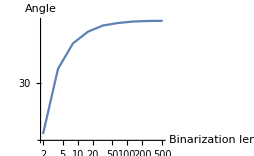
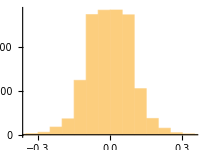
#### All Visualizations -Graphics- -Graphics- -Graphics--Graphics- -Graphics- -Graphics--Graphics--Graphics-